# Implementação do ORVF

```mathematica
Clear["Global`*"]
```

## Dados de Entrada

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined-> True,
Axes-> False,Frame-> True,Joined-> True,PlotRange->All];
```

```mathematica
FileNames["*.txt"];
```

```mathematica
omega=Flatten@ReadList["omega.txt"];
ytraco=Flatten[ReadList["YPAT.txt"]];
```

```mathematica
If[omega[[1]]==0,omega[[1]]=10^Floor[Log[10,omega[[2]]]]]; (*Evitar termino zero na frequencia*)
```

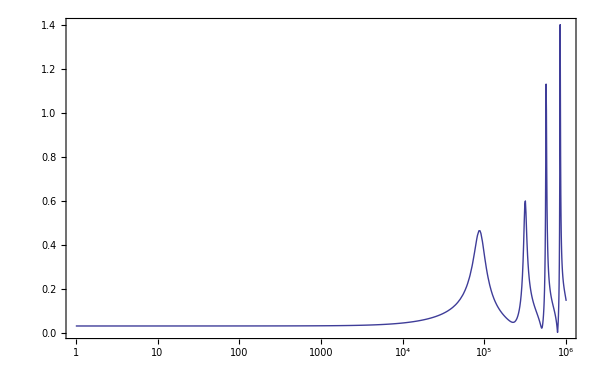

```mathematica
Grfun=ListLogLinearPlot[Transpose@{omega/(2 Pi),Abs[ytraco]}]
```

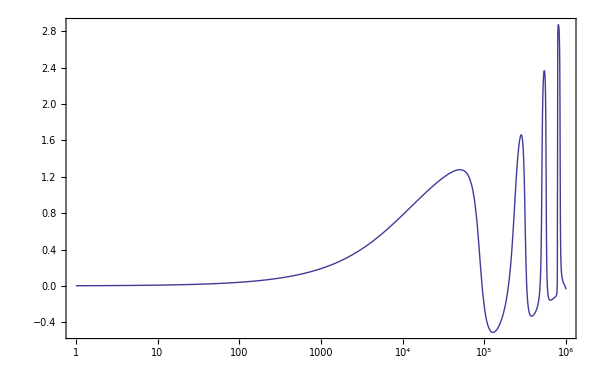

```mathematica
Grfun=ListLogLinearPlot[Transpose@{omega/(2 Pi),Arg[ytraco]}]
```

```mathematica
Max[Arg[ytraco]]
```

2.87154

```mathematica
Pi/2.
```

1.5708

### Polos Iniciais

```mathematica
fmax=Last@omega;
fmin=First@omega;
npolini=50;
```

```mathematica
polini=Flatten[Table[{-(ff)/100+ⅈ*(ff),-(ff)/100-ⅈ*(ff)},{ff,fmin,fmax,(fmax-fmin)/((npolini-1)/2)}]];
```

### Datos iniciais - VFit3 (Matlab)

```mathematica
MATLABpoles={polini};
MATLABs={omega*I};
MATLABf=ytraco;
MATLABweight={Table[1,{Length[omega]}]};
```

```mathematica
Export["ParaRVFMatlab/s.mat",MATLABs];
Export["ParaRVFMatlab/f.mat",MATLABf];
```

# Vector Fitting

### Funções Auxiliares

```mathematica
idx[polos_List]:=Module[{np,fun,ind},
np=Length[polos];
ind=0*Range[1,np];
fun=Map[Head,polos];
Do[If[fun[[mm]]==Complex,
If[mm==1,ind[[mm]]=1,
If[ind[[mm-1]]==0 ∨ ind[[mm-1]]==2 ,ind[[mm]]=1;ind[[mm+1]]=2,
ind[[mm]]=2]]],{mm,1,np}];
Return[ind]];

Aux[s_,p_List,index_List]:=With[
{np=Length[p]},
Table[If[index[[mm]]==0.,
(1/(s-p[[mm]])),If[index[[mm]]==1.,
(1/(s-p[[mm]])+1/(s-p[[mm+1]])),
(ⅈ/(s-p[[mm-1]])-ⅈ/(s-p[[mm]]))]],
{mm,np}]];

Aux2[s_,p_List,index_List]:=With[
{np=Length[p]},
Table[If[index[[mm]]==0.,
(Sqrt[2*Abs[p[[mm]]]])/(s-p[[mm]])*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-1}],
If[index[[mm]]==1.,
(Sqrt[-2*Re[p[[mm]]]])*(s-Abs[p[[mm]]])/((s-p[[mm]])*(s-p[[mm+1]]))*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-1}],
(Sqrt[-2*Re[p[[mm]]]])*(s+Abs[p[[mm]]])/((s-p[[mm-1]])*(s-p[[mm]]))*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-2}]]],
{mm,np}]];
```

# Cálculos dos Pólos com o RVF

```mathematica
RVFpolos[polos_List,freq_List,data_,termoD_:1,termoE_:1]:=Module[{npol,nfreq,ss,indices,Anum,UmS,Anum2,Af,AA,BB,XX,naux,Csigma,Azeros,Bzeros,Czeros,Dzeros,polaux,polosN,weight,Ws,RVF,i,j,q,r,AAA,BBB,AAAT,normas,Xaux,AAAaux,AAAscale,scale},
npol=Length[polos];
nfreq=Length[freq];
ss=ⅈ*freq;

indices=idx[polos];
Anum=Transpose[Aux[ss[[Range[nfreq]]],polos,indices]];

UmS=If[termoD==1∧termoE==1,{1,ss[[#]]}&/@Range[nfreq],
If[termoD==1∧termoE==0,{1}&/@Range[nfreq],
If[termoD==0∧termoE==1,{ss[[#]]}&/@Range[nfreq],{}&/@Range[nfreq]]]];
Anum2=-data*Anum;

weight=Table[1,{nfreq}];
Ws=Norm[Table[weight[[i]]*data[[i]],{i,1,nfreq}]]/nfreq;

RVF=Flatten[{Table[0,{npol+termoD+termoE}],Table[Sum[Re[Anum[[i,j]]],{i,1,nfreq}],{j,1,npol}],nfreq}]*Ws;
Af=Flatten[{Anum[[#]],UmS[[#]],Anum2[[#]],-data[[#]]}*weight[[#]]]&/@Range[nfreq];
AA=Join[Re[Af],Im[Af],{RVF}];
BB=Flatten[{0*Range[1,2*nfreq],nfreq}]*Ws;

AAA=Take[QRDecomposition[AA][[2]],-npol-1,-npol-1];
BBB=Take[QRDecomposition[AA][[1]],-npol-1].BB;

AAAT=Transpose[AAA];
normas=Norm[AAAT[[#]]]&/@Range[1,npol+1];
AAAaux=AAAT/normas;

AAAscale=Transpose[AAAaux];

Xaux=LeastSquares[AAAscale,BBB];
scale=1/normas;

XX=Xaux*scale;

Azeros=Table[0,{npol},{npol}];
Bzeros=Table[{0},{npol}];
Bzeros=Table[If[indices[[mm]]==0,Bzeros[[mm]]={1},If[indices[[mm]]==1,Bzeros[[mm]]={2},{0}]],{mm,npol}];
Czeros=Partition[XX[[Range[1,npol]]],1];
Dzeros=XX[[-1]];

Do[If[indices[[mm]]== 0,Azeros[[mm,mm]]=polos[[mm]],If[indices[[mm]]== 1,Azeros[[mm,mm]]=Re[polos[[mm]]];Azeros[[mm,mm+1]]=Im[polos[[mm]]];Azeros[[mm+1,mm]]=-Im[polos[[mm]]];Azeros[[mm+1,mm+1]]=Re[polos[[mm]]]],0],{mm,npol}];

polaux=Eigenvalues[Azeros-(Bzeros/Dzeros).Transpose[Czeros]];
polosN=-Abs[Re[polaux]]+ⅈ Im[polaux];

Return[polosN]]
```

# Cálculo dos Resíduos

### Cálculo dos Resíduos

```mathematica
res[polos_List,freq_List,data_List,termoD_:1.,termoE_:1.]:=Module[{npol,nfreq,ss,indices,AAnum,UUmS,AAf,AAff,AAffT,normas,BBff,XXff,resfim,dd,ee,naux,AAAaux,AAAscale,Xaux,scale},
npol=Length[polos];
nfreq=Length[freq];
ss=ⅈ*freq;

indices=idx[polos];

AAnum=Transpose[Aux[ss[[Range[nfreq]]],polos,indices]];

UUmS=If[termoD==1∧termoE==1,{1,ss[[#]]}&/@Range[nfreq],
If[termoD==1∧termoE==0,{1}&/@Range[nfreq],
If[termoD==0∧termoE==1,{ss[[#]]}&/@Range[nfreq],{}&/@Range[nfreq]]]];

AAf=Flatten[{AAnum[[#]],UUmS[[#]]}]&/@Range[nfreq];

AAff=ArrayFlatten[{{Re[AAf]},{Im[AAf]}}];
BBff=Flatten[{Re[data],Im[data]}];

naux=termoD+termoE;

AAffT=Transpose[AAff];
normas=Norm[AAffT[[#]]]&/@Range[1,npol+naux];
AAAaux=AAffT/normas;

AAAscale=Transpose[AAAaux];
Xaux=LeastSquares[AAAscale,BBff];
scale=1/normas;
XXff=Xaux*scale;

resfim=0*Range[1,npol];

Do[If[indices[[nm]]==0,resfim[[nm]]=XXff[[nm]],If[indices[[nm]]==1,resfim[[nm]]=XXff[[nm]]+ⅈ*XXff[[nm+1]];resfim[[nm+1]]=XXff[[nm]]-ⅈ*XXff[[nm+1]],0]],{nm,npol}];

If[termoD==1∧termoE==1,dd=XXff[[-2]];ee=XXff[[-1]],
If[termoD==1∧termoE==0,dd=XXff[[-1]];ee=0,
If[termoD==0∧termoE==1,dd=0;ee=XXff[[-1]],dd=0;ee=0]]];

Return[{resfim,dd,ee}]]
```

# Outros Calculos

```mathematica
calcelem[polos_List,residuos_List,omega_List,yElementos_,TermD_,TermE_,nres_]:=Module[{funcoes,Pontos,difRMS,dif,RMSD},
funcoes=Table[Sum[(residuos[[i,kk]]/(s-polos[[kk]])),{kk,Length[polos]}]+TermD[[i]]+s*TermE[[i]],{i,nres}];
Pontos=Transpose[Table[Map[(funcoes[[i]]/.s->#)&,ⅈ omega],{i,nres}]];
dif=Sqrt[Abs[(Pontos-yElementos)^2]/Length[omega]];
RMSD=Sqrt[Total[Abs[Pontos-yElementos]^2]/Length[omega]];
Return[{funcoes,Pontos,RMSD,dif}]]
```

```mathematica
calctraco[polos_List,residuos_List,omega_,data_,termoD_,termoE_]:=Module[{funcoes,Pontos,difRMS,dif},
funcoes=Table[Sum[(residuos[[kk]]/(s-polos[[kk]])),{kk,Length[polos]}]+termoD+s*termoE];
Pontos=Map[(funcoes/.s->#)&,ⅈ omega];
difRMS=Sqrt[Total[Abs[(Pontos-data)^2]]]/Sqrt[Length[omega]];
dif=Sqrt[Abs[(Pontos-data)^2]]/Sqrt[Length[omega]];
Return[{funcoes,Pontos,difRMS,dif}]]
```

```mathematica
descompmatr[Matr_]:=Module[{A=Matr},Select[Flatten[UpperTriangularize[A]],Abs[#]>0&]];
```

```mathematica
recompmatr[Matr_]:=Module[{A=Matr,ncond2,k,Mrecomp},
ncond2=Floor[0.5(-1+Sqrt[1+8*Length[A]])];
Mrecomp=Table[0,{ncond2},{ncond2}];
For[k=1,k<ncond2+1,k++,Mrecomp[[ncond2-k+1,ncond2-k+1;;ncond2]]=Take[A,-k];A=Take[A,Length[A]-k]];
Table[Mrecomp[[j,i]]=Mrecomp[[i,j]],{i,1,ncond2},{j,1,ncond2}];
Return[Mrecomp]]
```

```mathematica
recompmatrlarga[Matr_]:=Module[{A=Matr,Matr2},
Matr2=Table[0,{N[Max[Dimensions[A]]]}];
Table[Matr2[[j]]=recompmatr[A[[j]]],{j,1,N[Max[Dimensions[A]]]}];
Return[Matr2]]
```

```mathematica
descompmatrlarga[Matr_]:=Module[{A=Matr,Matr2},
Matr2=Table[0,{N[Max[Dimensions[A]]]}];
Table[Matr2[[j]]=descompmatr[A[[j]]],{j,1,N[Max[Dimensions[A]]]}];
Return[Matr2]]
```

```mathematica
recompmatrizesexport[polos_,residuos_,TermD_,TermE_,freq_]:=Module[{SERA,SERB,SERC,SERD,SERE,SERRsinconv,SERpoles,s,n,npol},
n=(Sqrt[1+8*N[Length[residuos]]]-1)/2;
s={freq};
SERA=SparseArray[DiagonalMatrix[Flatten[Table[{polos},{n}]]]//Chop];
npol=Length[polos];
SERB=Table[0,{n*npol},{n}];
Flatten[Table[SERB[[(j-1)*npol+i,j]]=1,{i,1,npol},{j,1,n}]];
{SERD,SERE}={recompmatr[TermD],recompmatr[TermE]};
SERRsinconv=Transpose[residuos];
SERC=Transpose[Flatten[recompmatrlarga[Transpose[residuos]],1]];
SERpoles=polos;
Return[{SERA,SERB,SERC,SERD,SERE,SERRsinconv,SERpoles,s}]]
```

# Fitting de ytraco (RVF, polos melhorados para Ynodal)

```mathematica
niter=25;
TemD=1.;
TemE=1;
ppolos=polini;
```

### Cálculo dos Pólos

```mathematica
AbsoluteTiming[Do[pp=RVFpolos[ppolos,omega,ytraco,TemD,TemE];ppolos=pp,{niter}]]
polostraco=ppolos;
```

{10.234375,Null}

### Cálculo dos Resíduos

```mathematica
AbsoluteTiming[{residuosRVFtr,TermDRVFtr,TermERVFtr}=res[polostraco,omega,ytraco,TemD,TemE]][[1]]
```

0.203125

```mathematica
{funcoesRVF,PontosRVFtr,difRMSRVFtr,difRVFtr}=calctraco[polostraco,residuosRVFtr,omega,ytraco,TermDRVFtr,TermERVFtr];
```

```mathematica
polostraco
```

{-1.50321×10^7,-103540.+7.12854×10^6 ⅈ,-103540.-7.12854×10^6 ⅈ,-2.12677×10^6+5.95289×10^6 ⅈ,-2.12677×10^6-5.95289×10^6 ⅈ,-65943.3+5.96802×10^6 ⅈ,-65943.3-5.96802×10^6 ⅈ,-39889.9+5.29639×10^6 ⅈ,-39889.9-5.29639×10^6 ⅈ,-1.9459×10^6+3.7961×10^6 ⅈ,-1.9459×10^6-3.7961×10^6 ⅈ,-366781.+3.82946×10^6 ⅈ,-366781.-3.82946×10^6 ⅈ,-3.78666×10^6,-42898.1+3.57144×10^6 ⅈ,-42898.1-3.57144×10^6 ⅈ,-1.75888×10^6+1.88774×10^6 ⅈ,-1.75888×10^6-1.88774×10^6 ⅈ,-85424.9+1.97098×10^6 ⅈ,-85424.9-1.97098×10^6 ⅈ,-1.63442×10^6,-1.15112×10^6,-761500.,-92804.5+542289. ⅈ,-92804.5-542289. ⅈ,-362912.,-339369.,-173374.,-152945.,-81061.7,-69746.1,-36821.,-31019.9,-16275.1,-13395.6,-7017.7,-5598.53,-2968.88,-2253.07,-1256.29,-866.395,-563.92,-314.691,-266.64,-107.72,-105.952,-34.5703,-32.0398,-7.66442,-7.5552}

# Graficos Finales

```mathematica
GrRVFtr=ListLogLogPlot[Transpose@{omega/(2 Pi),Abs[PontosRVFtr]},PlotStyle->{Orange,Dashed}];
Grfuntr=ListLogLogPlot[Transpose@{omega/(2 Pi),Abs[ytraco]},PlotStyle->{Black,Thick}];
```

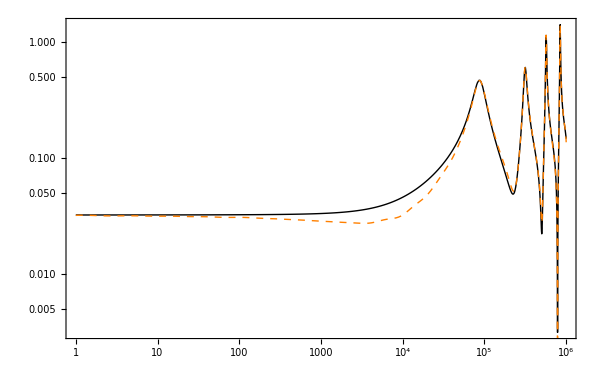

```mathematica
Show[Grfuntr,GrRVFtr]
```

```mathematica
ErroRVFptr=ListLogLogPlot[difRVFtr,PlotStyle->{Orange,Dashed,Thick}];
ErroRVFftr=ListLogLogPlot[Transpose@{omega/(2 Pi),difRVFtr},PlotStyle->{Orange,Thin}];
```

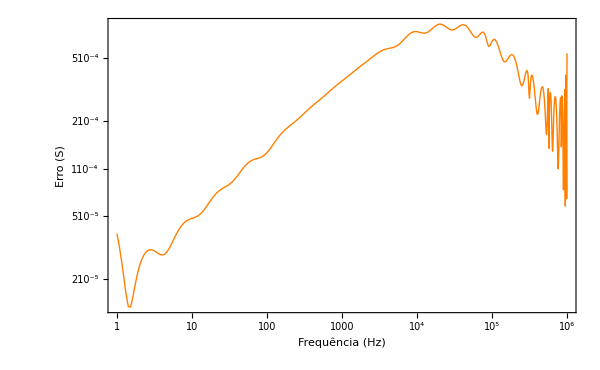

```mathematica
Show[ErroRVFftr,FrameLabel->{"Frequência (Hz)","Erro (S)"},LabelStyle->{Large,Bold}]
```

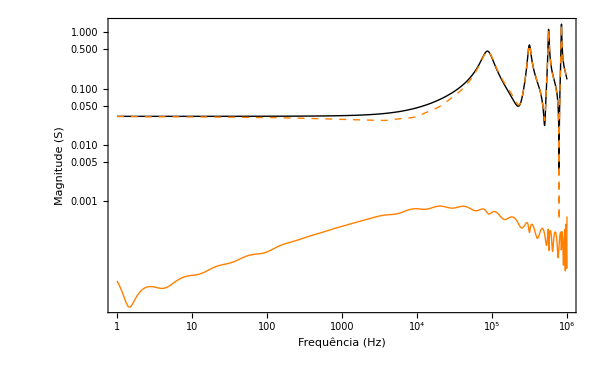

```mathematica
Show[Grfuntr,GrRVFtr,ErroRVFftr,FrameLabel->{"Frequência (Hz)","Magnitude (S)"},LabelStyle->{Large,Bold},PlotRange->All]
```

```mathematica
Tabela=Table[{{Sort[polostraco]}}];
TableForm[Tabela,TableHeadings->{None,{"polosRVF"}},TableAlignments->Center];
```

```mathematica
Ys=recompmatrlarga[PontosRVFElem];
evals=Map[Eigenvalues,Re[Ys]];
Min[evals]
```

Table::iterb: Iterator {-∞} does not have appropriate bounds.

Table::iterb: Iterator {j, 1, -∞} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Re[Eigenvalues[Table[0,{-∞}]]]